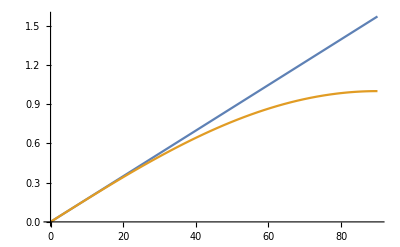

```mathematica
Plot[{x °,Sin[x °]},{x,0,90}]
```

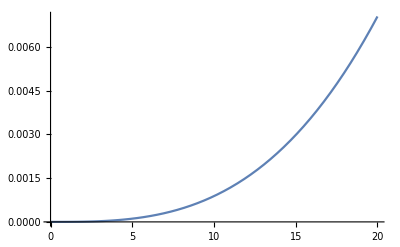

```mathematica
Plot[{x °-Sin[x °]},{x,0,20}]
```

```mathematica
Table[{x,x °-Sin[x °]},{x,0,25,1.}]//TableForm
```

0. | 0.
1. | 8.86083×10^-7
2. | 7.08834×10^-6
3. | 0.0000239213
4. | 0.0000566963
5. | 0.00011072
6. | 0.000191292
7. | 0.000303704
8. | 0.000453239
9. | 0.000645168
10. | 0.000884748
11. | 0.00117722
12. | 0.00152782
13. | 0.00194175
14. | 0.0024242
15. | 0.00298034
16. | 0.00361532
17. | 0.00433427
18. | 0.00514227
19. | 0.0060444
20. | 0.00704571
21. | 0.00815119
22. | 0.00936584
23. | 0.0106946
24. | 0.0121424
25. | 0.0137141

```mathematica
(*MAS*)
ecd=θ''[t]+ω^2 θ[t]==0;
```

```mathematica
DSolve[ecd,θ,t]
```

{{θ→Function[{t},C[1] Cos[t ω]+C[2] Sin[t ω]]}}

```mathematica
sol1[t_]=θ[t]/.First@DSolve[ecd,θ,t]
```

C[1] Cos[t ω]+C[2] Sin[t ω]

```mathematica
Solve[{sol1[0]==θ0, sol1'[0]==θp0},{C[1],C[2]}]
```

{{C[1]→θ0,C[2]→θp0/ω}}

```mathematica
DSolve[{ecd,θ[0]==θ0,θ'[0]==θp0},θ,t]
```

{{θ→Function[{t},(θ0 ω Cos[t ω]+θp0 Sin[t ω])/ω]}}

```mathematica
soln[t_]=θ[t]/.First@NDSolve[{ecd/.ω->1,θ[0]==15°,θ'[0]==0},θ[t],{t,0,10}]
```

InterpolatingFunction[…][t]

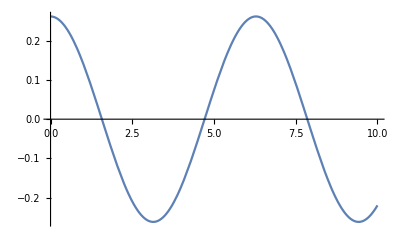

```mathematica
Plot[soln[t],{t,0,10}]
```

```mathematica
Manipulate[Plot[θ[t]/.First@NDSolve[{ecd/.ω->Sqrt[9.81/l],θ[0]==15°,θ'[0]==0},θ[t],{t,0,10}]/.t->T,{T,0,10}],{l,.1,10,.1}]
```

NDSolve::deqn: Equation or list of equations expected instead of ecd in the first argument {ecd,θ[0]==15 °,θ'[0]==0}.

ReplaceAll::reps: {ecd,θ[0]==15 °,θ'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {ecd,θ[0.]==0.261799,θ'[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of ecd in the first argument {ecd,θ[0]==15 °,θ'[0]==0}.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

```mathematica
ecd2=θ''[t]+ω^2 Sin[θ[t]]==0;
```

```mathematica
Manipulate[Plot[{(θ[t]/.First@NDSolve[{ecd/.ω->Sqrt[9.81/l],θ[0]==angulo °,θ'[0]==0},θ[t],{t,0,10}]),(θ[t]/.First@NDSolve[{ecd2/.ω->Sqrt[9.81/l],θ[0]==angulo °,θ'[0]==0},θ[t],{t,0,10}])}/.t->T,{T,0,10}],{{l,1},.1,10,.1},{{angulo,15},1,45,1}]
```

```mathematica
Manipulate[Plot[{(θ[t]/.First@NDSolve[{ecd/.ω->Sqrt[9.81/l],θ[0]==angulo °,θ'[0]==0},θ[t],{t,0,10}])-(θ[t]/.First@NDSolve[{ecd2/.ω->Sqrt[9.81/l],θ[0]==angulo °,θ'[0]==0},θ[t],{t,0,10}])}/.t->T,{T,0,10}],{{l,1},.1,10,.1},{{angulo,15},1,45,1}]
```

```mathematica
Manipulate[Plot[{(θ[t]/.First@NDSolve[{ecd/.ω->Sqrt[9.81/l],θ[0]==angulo °,θ'[0]==0},θ[t],{t,0,tfin}]),(θ[t]/.First@NDSolve[{ecd2/.ω->Sqrt[9.81/l],θ[0]==angulo °,θ'[0]==0},θ[t],{t,0,tfin}])}/.t->T,{T,tfin-10,tfin}],{{l,1},.1,10,.1},{{angulo,15},1,45,1},{{tfin,80},10,100}]
```

```mathematica
p[q_,r_,r1_]:=q/Norm[r-r1]
```

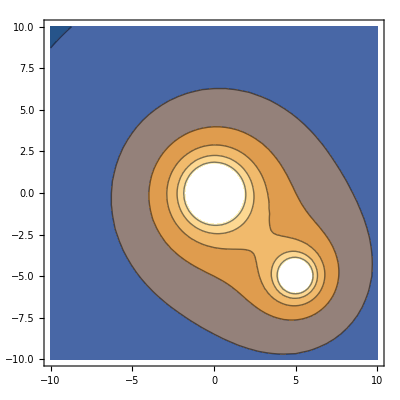

```mathematica
ContourPlot[p[10,{x,y},{0,0}]+p[5,{x,y},{5,-5}],{x,-10,10},{y,-10,10}]
```

```mathematica
Grad[p[10,{x,y},{0,0}],{x,y}]
```

{-(10 Abs[x] Abs'[x])/((Abs[x]^2+Abs[y]^2)^(3/2)),-(10 Abs[y] Abs'[y])/((Abs[x]^2+Abs[y]^2)^(3/2))}

```mathematica
e[q_,r_,r1_]:=q(r-r1)/Norm[r-r1]^3
```

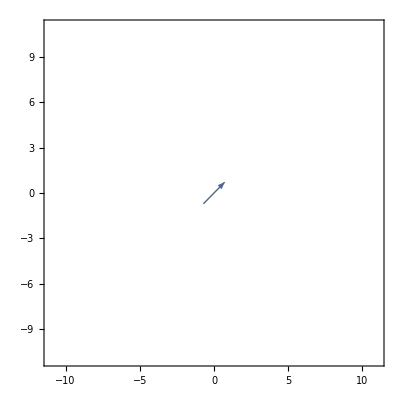

```mathematica
VectorPlot[e[10,{x,y},{0,0}],{x,-10,10},{y,-10,10}]
```

```mathematica
e[10,{2,2},{0,0}]
```

{5/(4 √2),5/(4 √2)}

```mathematica
VectorPlot[Grad[p[10,{x,y},{0,0}],{x,y}],{x,-10,10},{y,-10,10}]
```

-Graphics-